```mathematica
ClearAll["Global`*"];
```

```mathematica
lo=0.5; (*m*)
```

### Wykorzystanie prawa Hooka do obliczenia ciezaru zawieszonego na drucie ( "Q" ). “Δl” - przyrost dlugosci drutu, “S” - pole przekroju poprzecznego drutu, “Ey” - modul Yunga metalu, z ktorego zrobiony jest drut.

```mathematica
r1=Solve[Δl/lo==Q/S×1/Ey,Q];
```

### Obliczenie sily naciagu ( "F_n" ) dzialajacej na drut. “α” - kat jaki tworzy drut z kierunkiem pionu.

```mathematica
Fn =Sqrt[Q^2+ (Tan[α °]×Q)^2]/.r1[[1,1]];
```

### Obliczenie wydluzenia wzglednego ( "ϵ" ) wywolanego przez sile naciagu.

```mathematica
ϵ=Fn/S×1/Ey//Simplify//PowerExpand;
```

### Sporzadzenie wykresu obrazujacego zaleznosc wydluzenia wzglednego od kata “α” dla Δl = .5 cm.

```mathematica
rys1=Plot[ϵ/.Δl->0.005,{α,30,60},
BaseStyle->{FontFamily->"Times", FontSlant->"Italic", FontSize->12},
AxesLabel->{"α, deg","ϵ, 1"},
DisplayFunction -> Identity,
PlotRange->All,
PlotStyle->{RGBColor[1,0,0],Thickness[0.006]}];
```

### Sporzadzenie wykresu obrazujacego zaleznosc wydluzenia wzglednego od kata “α” dla Δl = 1 cm.

```mathematica
rys2=Plot[ϵ/.Δl->0.01,{α,30,60},
BaseStyle->{FontFamily->"Times", FontSlant->"Italic", FontSize->12},
DisplayFunction -> Identity,
AxesLabel->{"α, deg","ϵ, 1"},
PlotRange->All,
PlotStyle->{RGBColor[0,1,0],Thickness[0.006]}];
```

```mathematica
rys3=Plot[ϵ/.Δl->0.02,{α,30,60},
BaseStyle->{FontFamily->"Times", FontSlant->"Italic", FontSize->12},
DisplayFunction -> Identity,
AxesLabel->{"α, deg","ϵ, 1"},

PlotRange->All,
Label
PlotStyle->{RGBColor[0,0,1],Thickness[0.006]}];
```

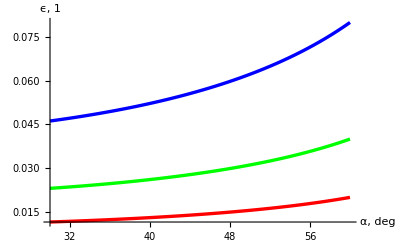

```mathematica
Show[rys1,rys3, rys2,  DisplayFunction->$DisplayFunction]
```